```mathematica
Counting of sparsity :
```

Here we discuss how the sparsity varies with the dimension of the matrix.

### Two qubit

We start with a two qubit system where the initial density matrix is,

```mathematica
Clear[RHO,a,b,PauliUnitary]
Clear[a1,a2,θ]
RHO[a1_,a2_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}}]
L = Length[ArrayRules[SparseArray[RHO[a,b]]]/.Rule->List]-1;
Sparsity = L/(2^2)^2;
Hint = {{0,0,0,0},{0,0,I,0},{0,-I, 0,0},{0,0,0,0}};
U=MatrixExp[- I Hint θ]//FullSimplify
PauliUnitary[k_]:= KroneckerProduct[IdentityMatrix[1],UPauli[k],IdentityMatrix[1]] 
UPauli[k_]:= MatrixExp[- I PauliMatrix[k]]//FullSimplify
$Assumptions ={θ,ϕ,a1,a2} ∈Reals
RHOT = PauliUnitary[1].RHO[a1,a2].Transpose[PauliUnitary[1]]//FullSimplify;
KroneckerProduct[Identity[1],PauliMatrix[1]]
```

{{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}}

(θ|ϕ|a1|a2)∈ℝ

Dot::dotsh: Tensors {{Cos[1],-ⅈ Sin[1]},{-ⅈ Sin[1],Cos[1]}} and {{(1-a1) (1-a2),0,0,0},{0,(1-a1) a2,0,0},{0,0,a1 (1-a2),0},{0,0,0,a1 a2}} have incompatible shapes.

Dot::dotsh: Tensors {{(1-a1) (1-a2),0,0,0},{0,(1-a1) a2,0,0},{0,0,a1 (1-a2),0},{0,0,0,a1 a2}} and {{Cos[1],-ⅈ Sin[1]},{-ⅈ Sin[1],Cos[1]}} have incompatible shapes.

KroneckerProduct::rect: Nonrectangular array encountered.

KroneckerProduct[1,{{0,1},{1,0}}]

```mathematica
cde3\
```

```mathematica
SparseArray[RHOT];
Lt = Length[ArrayRules[SparseArray[RHOT]]/.Rule->List]-1;
SparsityT = Lt/(2^2)^2 ;
Print[16]
Print[ L]
Print[Lt]
Print[N[Sparsity]]
Print[N[SparsityT]]
TraceSystem[RHOT,2]//FullSimplify
Pop[a1_,a2_,θ_
]:= 1/2 (a1+a2+(a1-a2) Cos[2 θ]);
WorkExtractable= Temp[Pop[at,a2,θ]]((1-Pop[a1,adummy,θ])Log[(1-Pop[a1,adummy,θ])/(1-Pop[at,a2,θ])]  + (Pop[a1,adummy,θ])Log[(Pop[a1,adummy,θ])/(Pop[at,a2,θ])]  )-Temp[at]((1-a1)Log[(1-a1)/(1-at)]  + (a1)Log[(a1)/(at)]  );
For[Work= WorkExtractable;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];at=RandomReal[{0.0001,0.4999}];adummy=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= WorkExtractable; If[Work>0,Print[Work],Null];Clear[Work,a1,a2,at,θ]]
```

Clear::ssym: RHO.Work is not a symbol or a string.

KroneckerProduct::rect: Nonrectangular array encountered.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{1-a,0},{0,a}},{{{1,-2},0},{0,{0,3}}}]].

ArrayRules::rect: Nonrectangular array encountered.

{{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}}

(θ|ϕ|a1|a2)∈ℝ

Dot::dotsh: Tensors {{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}} and {{(1-a1) (1-a2),0,0,0},{0,(1-a1) a2,0,0},{0,0,a1 (1-a2),0},{0,0,0,a1 a2}} have incompatible shapes.

Dot::dotsh: Tensors {{(1-a1) (1-a2),0,0,0},{0,(1-a1) a2,0,0},{0,0,a1 (1-a2),0},{0,0,0,a1 a2}} and {{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}} have incompatible shapes.

SparseArray::list: List expected at position 1 in SparseArray[{{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}}.{{(-1+a1) (-1+a2),0,0,0},{0,a2-a1 a2,0,0},{0,0,a1-a1 a2,0},{0,0,0,a1 a2}}.{{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}}].

ArrayRules::rect: Nonrectangular array encountered.

16

0

0

0.

0.

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

{{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}}.{{(-1+a1) (-1+a2),0,0,0},{0,a2-a1 a2,0,0},{0,0,a1-a1 a2,0},{0,0,0,a1 a2}}.{{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}}

0.0347876

0.0659128

0.0554759

0.830837

0.0244158

0.15012

0.0327844

0.0145658

0.0452402

0.0510971

0.00252075

0.0192539

0.093971

0.0663017

0.024619

0.00206227

0.00465454

1.40642

0.127786

0.0168943

0.0102077

0.00985564

0.103802

0.0011367

0.00153111

0.019865

0.000173941

0.00840514

15.8665

0.0782707

0.379289

0.0116671

0.103816

0.125494

0.0343512

0.00188956

0.0239509

0.00972607

0.000546617

0.00791905

0.00789595

0.028405

0.0117876

0.0126458

2.76784

0.0783934

0.0994474

0.797692

0.0625088

0.00798953

0.0547849

0.0869533

0.00520976

0.00199781

0.0196081

0.136882

0.0000880251

0.190859

0.00467069

0.0166055

0.0367022

0.0316849

1.79986

0.0179171

0.0203161

0.00342179

0.000189336

0.00188309

0.000642034

0.0413144

0.00119741

0.0147763

0.00412346

3.46595×10^-6

0.00428221

0.00708821

0.0562059

0.0110632

0.150503

0.0246685

0.000836826

0.00769103

0.000954018

7.14935×10^-7

0.0349948

0.00686341

0.235647

0.0318026

0.0275395

0.00434079

0.107103

0.00036747

3.56897×10^-8

0.0268644

0.0316643

0.00309286

0.0508617

0.0532153

12.5521

0.00371184

0.00240123

0.209727

0.0013048

0.0511589

0.000284721

0.00146307

0.00401222

0.00359028

0.115497

0.0213212

0.0642331

0.00795047

0.791878

```mathematica
cd\00de3
```

```mathematica
cd\0e30
```

```mathematica
Tinitial = TraceSystem[RHO[a1,a2],{1}];
Tfinal = TraceSystem[RHOTmachtrial,{1}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify
```

```mathematica
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
```

```mathematica
RHOsysInitial= TraceSystem[RHO[a1,a2],{2}]//FullSimplify;
RHOmachInitial= TraceSystem[RHO[a2,a2],{2}]//FullSimplify;
```

```mathematica
RHOsysFinal= TraceSystem[RHOTsystrial,{2}]//FullSimplify;
```

```mathematica
A1 =Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial = Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]- Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
```

```mathematica
Clear[a1,a2,t,Wex]
```

```mathematica
Wex = WFinal-WInitial;
```

ArcTanh[1-2 a2] (a1+a2+(a1-a2) Cos[2 t])+(-1+a1) Log[1-a1]-a1 Log[a1]-Log[1-a2]-(-1+a1) Log[1-a2]+a1 Log[a2]+1/2 ((a1+a2+(a1-a2) Cos[2 t]) Log[1/2 (a1+a2+(a1-a2) Cos[2 t])]-(-2+a1+a2+(a1-a2) Cos[2 t]) Log[1/2 (2-a1-a2+(-a1+a2) Cos[2 t])])

```mathematica
Clear[a1,a2,t,Work]
For[Work= Wex;i=1, i<15,i++,Work=Wex;a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];t=RandomReal[{0,2π}];
Work= Wex; Print[Work];Clear[Work,a1,a2,t]]
```

### Three qubit

We now look at the sparsity of three qubits

```mathematica
n=3;
Clear[RHO,a1,a2,a3,RHOT]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
```

```mathematica
RHOlabel = {{A1,0,0,0,0,0,0,0},{0,A2,0,0,0,0,0,0},{0,0,A3,0,0,0,0,0},{0,0,0,A4,0,0,0,0},{0,0,0,0,A5,0,0,0},{0,0,0,0,0,A6,0,0},{0,0,0,0,0,0,A7,0},{0,0,0,0,0,0,0,A8}};
L = Length[ArrayRules[SparseArray[RHO[a,b,c]]]/.Rule->List]-1;
Sparsity = L/(2^n)^2;
Hint = -{{0,0,0,0,0,0,0,0},{0,0,I ,0,I ,0,0,0},{0,- I  ,0,0,I ,0,0,0},{0,0,0,0,0,I ,I ,0},{0,-I ,-I ,0,0,0,0,0},{0,0,0,-I ,0,0,I ,0},{0,0,0,-I ,0,-I ,0,0},{0,0,0,0,0,0,0,0}};
```

KroneckerProduct::rect: Nonrectangular array encountered.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{1-a,0},{0,a}},{{{1,-2},0},{0,{0,3}}},{{{0,-1,-2,-3},0},{0,{1,2,3,4}}}]].

ArrayRules::rect: Nonrectangular array encountered.

```mathematica
HintEnergysubsp1[G1_,G2_,G3_] := -{{0,0,0,0,0,0,0,0},{0,0,I G1,0,I G2,0,0,0},{0,- I G1 ,0,0,I G3,0,0,0},{0,0,0,0,0,0,0,0},{0,-I G2,-I G3,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
HintEnergysubsp2 [F1_,F2_,F3_] := -{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0 ,0,0,0,0,0,0},{0,0,0,0,0,I F1,I F2,0},{0,0,0,0,0,0,0,0},{0,0,0,-I F1,0,0,I F3,0},{0,0,0,-I F2,0,-I F3,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
U1=MatrixExp[- I HintEnergysubsp1[1,0,0] θ]//FullSimplify;
U2=MatrixExp[- I HintEnergysubsp1[0,1,0] θ]//FullSimplify;
U3=MatrixExp[- I HintEnergysubsp1[0,0,1] θ]//FullSimplify;
U4=MatrixExp[- I HintEnergysubsp1[1,1,0] θ]//FullSimplify;
U5=MatrixExp[- I HintEnergysubsp1[1,0,1] θ]//FullSimplify;
U6=MatrixExp[- I HintEnergysubsp1[0,1,1] θ]//FullSimplify;
U7=MatrixExp[- I HintEnergysubsp1[1,1,1] θ]//FullSimplify;
U8=MatrixExp[- I HintEnergysubsp2[1,0,0] θ]//FullSimplify;
U9=MatrixExp[- I HintEnergysubsp2[0,1,0] θ]//FullSimplify;
U10=MatrixExp[- I HintEnergysubsp2[0,0,1] θ]//FullSimplify;
U11=MatrixExp[- I HintEnergysubsp2[1,1,0] θ]//FullSimplify;
U12=MatrixExp[- I HintEnergysubsp2[1,0,1] θ]//FullSimplify;
U13=MatrixExp[- I HintEnergysubsp2[0,1,1] θ]//FullSimplify;
U14=MatrixExp[- I HintEnergysubsp2[1,1,1] θ]//FullSimplify;
```

```mathematica
U=MatrixExp[- I Hint θ]//FullSimplify;
RHOT = U.RHO[a1,a2,a3].Transpose[U]//FullSimplify;
RHOTT = U.RHOT.Transpose[U];
```

```mathematica
SparseArray[RHOT];
Lt = Length[ArrayRules[SparseArray[RHOT]]/.Rule->List]-1;
SparsityT = Lt/(2^n)^2 ;
Print[64]
Print[ L]
Print[Lt]
Print[N[Sparsity]]
Print[N[SparsityT]]
MatrixForm[RHOTlabel]//FullSimplify;
MatrixForm[U]//FullSimplify;
```

64

0

20

0.

0.3125

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,Utrial,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
Utrial=MatrixExp[- I Hint  t]//FullSimplify;
RHOTsystrial = Utrial.RHO[a1,a2,a3].Transpose[Utrial]//FullSimplify;
RHOTmachtrial = Utrial.RHO[a2,a2,a3].Transpose[Utrial]//FullSimplify;
```

```mathematica
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
```

```mathematica
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
```

```mathematica
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOmachInitial= TraceSystem[RHO[a2,a2,a3],{2,3}]//FullSimplify;
```

```mathematica
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
```

```mathematica
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
```

```mathematica
For[Work= Wex;i=1, i<50000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];t=RandomReal[{0,2π}];
Work= Wex; If[Work>0,Print[Work],Null];Clear[Work,a1,a2,a3,t]]
```

Unitary1

```mathematica
Temp[h_]:= Temp[h] = 1/(Log[(1-h)/h]);
```

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U1.RHO[a1,a2,a3].Transpose[U1]//FullSimplify;
RHOTmachtrial = U1.RHO[a2,a2,a3].Transpose[U1]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

```mathematica
LinguisticAssistant
```

Unitary2

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U2.RHO[a1,a2,a3].Transpose[U2]//FullSimplify;
RHOTmachtrial = U2.RHO[a2,a2,a3].Transpose[U2]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 3

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U3.RHO[a1,a2,a3].Transpose[U3]//FullSimplify;
RHOTmachtrial = U3.RHO[a2,a2,a3].Transpose[U3]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 4

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U4.RHO[a1,a2,a3].Transpose[U4]//FullSimplify;
RHOTmachtrial = U4.RHO[a2,a2,a3].Transpose[U4]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary5

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U5.RHO[a1,a2,a3].Transpose[U5]//FullSimplify;
RHOTmachtrial = U5.RHO[a2,a2,a3].Transpose[U5]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 6

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U6.RHO[a1,a2,a3].Transpose[U6]//FullSimplify;
RHOTmachtrial = U6.RHO[a2,a2,a3].Transpose[U6]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 7

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U7.RHO[a1,a2,a3].Transpose[U7]//FullSimplify;
RHOTmachtrial = U7.RHO[a2,a2,a3].Transpose[U7]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 8

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U8.RHO[a1,a2,a3].Transpose[U8]//FullSimplify;
RHOTmachtrial = U8.RHO[a2,a2,a3].Transpose[U8]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 9

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U9.RHO[a1,a2,a3].Transpose[U9]//FullSimplify;
RHOTmachtrial = U9.RHO[a2,a2,a3].Transpose[U9]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<50000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 10

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U10.RHO[a1,a2,a3].Transpose[U10]//FullSimplify;
RHOTmachtrial = U10.RHO[a2,a2,a3].Transpose[U10]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<50000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 11

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U11.RHO[a1,a2,a3].Transpose[U11]//FullSimplify;
RHOTmachtrial = U11.RHO[a2,a2,a3].Transpose[U11]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<50000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 12

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U12.RHO[a1,a2,a3].Transpose[U12]//FullSimplify;
RHOTmachtrial = U12.RHO[a2,a2,a3].Transpose[U12]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 13

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U13.RHO[a1,a2,a3].Transpose[U13]//FullSimplify;
RHOTmachtrial = U13.RHO[a2,a2,a3].Transpose[U13]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 14

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U14.RHO[a1,a2,a3].Transpose[U14]//FullSimplify;
RHOTmachtrial = U14.RHO[a2,a2,a3].Transpose[U14]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]3
```

We suspect that the rise in the non zero elements comes from the pair-wise correlations one must now consider. Recall that for the two qubit case, the hermiticity of the density matrices implied that to each correlation that would develop the number of non-zero elements in the matrix goes up by two. SImilarly now, considering all the interactions that can introduce correlations i.e. both in energy subspace 1 and energy subspace 2, we have 6 interactions which implies that the number of nonzero elements goes up by 12 and indeed that is the trend that the matrix follows. Based on this, we expect that in the four qubit case the number of non zero elements would go up by 54 elements (non zero elements initially = 16, total elements = 54+16=70 which gives sparsity to be 0.273438).

### Four qubit

We now look at the sparsity of four qubits

```mathematica
n=4;
RHO[a1_,a2_,a3_,a4_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}}]
```

```mathematica
L = Length[ArrayRules[SparseArray[RHO[a,b,c,d]]]/.Rule->List]-1;
Sparsity = L/(2^n)^2;
```

```mathematica
HintEnergysubsp14Q = SparseArray[{{2,3}->I,{3,2}->-I,{2,5}->I,{5,2}->-I,{2,9}->I,{9,2}->-I,{3,5}->I,{5,3}->-I,{3,9}->I,{9,3}->-I,{5,9}->I,{9,5}->-I},{16,16}];
HintEnergysubsp24Q = SparseArray[{{4,6}->I,{4,7}->I,{4,10}->I,{4,11}->I,{4,13}->I,{6,4}->-I,{7,4}->-I,{10,4}->-I,{11,4}->-I,{13,4}->-I,{6,7}->I,{6,10}->I,{6,11}->I,{6,13}->I,{7,6}->-I,{10,6}->-I,{11,6}->-I,{13,6}->-I,{7,10}->I,{7,11}->I,{7,13}->I,{10,7}->-I,{11,7}->-I,{13,7}->-I,{10,11}->I,{10,13}->I,{11,10}->-I,{13,10}->-I,{11,13}->I,{13,11}->-I},{16,16}];
HintEnergysubsp34Q = SparseArray[{{8,12}->I,{8,14}->I,{8,15}->I,{12,8}->-I,{14,8}->-I,{15,8}->-I,{12,14}->I,{12,15}->I,{14,15}->I,{14,12}->-I,{15,14}->-I,{15,12}->-I},{16,16}];
```

```mathematica
U1=MatrixExp[- I HintEnergysubsp14Q  θ]//FullSimplify;
```

```mathematica
U2=MatrixExp[- I HintEnergysubsp24Q  θ]//FullSimplify;
```

```mathematica
U3=MatrixExp[- I HintEnergysubsp34Q  θ]//FullSimplify;
```

4

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,Utrial,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_,a4_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}}]
HintTrial = SparseArray[{{8,12}->I,{12,8}->-I},{16,16}];
Utrial=MatrixExp[- I HintTrial  t]//FullSimplify;
RHOTsystrial = Utrial.RHO[a1,a2,a3,a4].Transpose[Utrial]//FullSimplify;
RHOTmachtrial = Utrial.RHO[a3,a3,a3,a4].Transpose[Utrial]//FullSimplify;
```

```mathematica
RHOT1=TraceSystem[RHOTsystrial,{2,3,4}]//FullSimplify
RHOT2=TraceSystem[RHOTsystrial,{1,3,4}]//FullSimplify
RHOT3=TraceSystem[RHOTsystrial,{1,2,4}]//FullSimplify
RHOT4=TraceSystem[RHOTsystrial,{1,2,3}]//FullSimplify
```

{{0.753738+0.000128346 Cos[2 t],0},{0,0.246262-0.000128346 Cos[2 t]}}

{{0.737724-0.000128346 Cos[2 t],0},{0,0.262276+0.000128346 Cos[2 t]}}

{{0.889078,0},{0,0.110922+2.71051×10^-20 Cos[2 t]}}

{{0.85777,0},{0,0.14223+2.71051×10^-20 Cos[2 t]}}

```mathematica
Clear[a1,a4,a2,a3]
Tinitial = TraceSystem[RHO[a1,a2,a3,a4],{1,2,4}];
Tfinal = TraceSystem[RHOTsystrial,{1,2,4}]//FullSimplify
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
```

{{1-a3,0},{0,a3}}

Under such a mechanism things are actually gibbs preserving. So the temperature maybe takes from eithe the fisrt or the second machine qubits.

```mathematica
RHOthInitial = KroneckerProduct[{{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}},{{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}}];
RHOthInitial1Q ={{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}}//FullSimplify
```

{{0.889078,0},{0,0.110922}}

```mathematica
RHOsysInitial= TraceSystem[RHO[a1,a2,a3,a4],{2,3,4}];
```

```mathematica
RHOthFinal = KroneckerProduct[{{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}},{{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}}];
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3,4}];
RHOthFinal1Q ={{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}}//FullSimplify//FullSimplify
```

{{1-a3,0},{0,a3}}

0.246133

0.262404

0.110922

0.14223

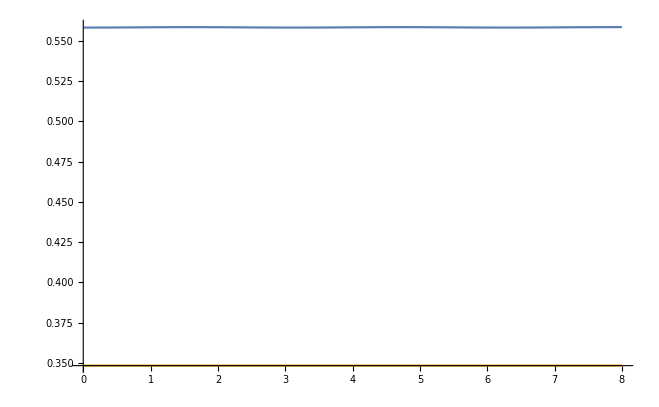

0.301437

0.0132203

0.275558

0.208278

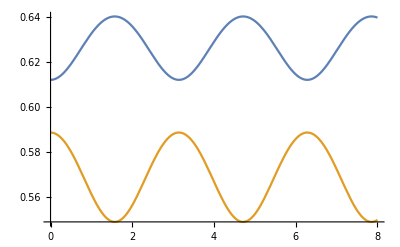

```mathematica
a1=0.24613345228581818
a2=0.26240396463534843
a3=0.11092212990736317
a4=0.14223010978606854
Plot[{-Tr[RHOsysFinal.MatrixLog[RHOsysFinal]],-Tr[RHOthFinal1Q.MatrixLog[RHOthFinal1Q]]},{t,0,8},PlotRange->Automatic]
```

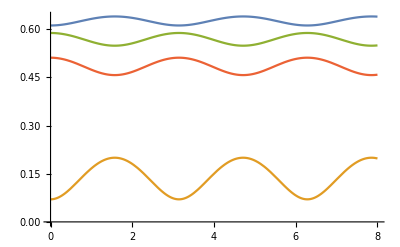

```mathematica
Plot[{-Tr[RHOT1.MatrixLog[RHOT1]],-Tr[RHOT2.MatrixLog[RHOT2]],-Tr[RHOT3.MatrixLog[RHOT3]],-Tr[RHOT4.MatrixLog[RHOT4]]},{t,0,8},PlotRange->Automatic]
```

```mathematica
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal1Q]]//FullSimplify;
```

```mathematica
WFinal=A1-A2;
```

```mathematica
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial1Q]]//FullSimplify;
Wex = WFinal-WInitial;
Wex
```

-(-2 a1 ArcTanh[1-2 a1]+2 a1 ArcTanh[1-2 a3]+Log[1-a1]-Log[1-a3])/Log[-1+1/a3]-(ArcTanh[1-2 a3] (-2 a1+(a1-a2) a3 a4+(-a1+a2) a3 a4 Cos[2 t])+Log[1-a3])/Log[-1+1/a3]+(-2 ArcTanh[1-2 a1+(a1-a2) a3 a4+(-a1+a2) a3 a4 Cos[2 t]] (2 a1+(-a1+a2) a3 a4+(a1-a2) a3 a4 Cos[2 t])+2 Log[1/2 (2-2 a1+(a1-a2) a3 a4+(-a1+a2) a3 a4 Cos[2 t])])/(2 Log[-1+1/a3])

```mathematica
a1=0.0799509
a2=0.36807803959358554
a3=0.15999
a4=0.38506791800464046
Wex
```

0.1

0.2

0.4

0.01

-0.783805-(0.26 Log[0.06 (-1.766-0.234 Cos[2 t]) (-2.156+0.156 Cos[2 t])]+Log[0.04 (1.766+0.234 Cos[2 t])^2] (0.00812+0.01188 Cos[t]^2+0.00288 Sin[t]^2)+Log[0.09 (2.156-0.156 Cos[2 t])^2] (0.72 (0.996+0.004 Cos[t]^2)+0.01188 Sin[t]^2))/Log[-1-5./(-1.766-0.234 Cos[2 t])]+(-0.510722+Log[1/2 (0.031+0.009 Cos[2 t])] (0.00812+0.01188 Cos[t]^2+0.00288 Sin[t]^2)+Log[1/2 (1.449-0.009 Cos[2 t])] (0.72 (0.996+0.004 Cos[t]^2)+0.01188 Sin[t]^2))/Log[-1-5./(-1.766-0.234 Cos[2 t])]

this works

0.13641

0.405972

0.122006

0.486451

this works

0.246133

0.262404

0.110922

0.14223

this works

0.452538

0.468262

0.125051

0.171749

this works

0.152987

0.00394917

0.490848

0.150658

this works

0.0333742

0.00955519

0.497879

0.445179

this works

0.129062

0.360888

0.125534

0.412339

this works

0.110909

0.186858

0.0177965

0.28826

this works

0.255149

0.476403

0.109427

0.387217

this works

0.080267

0.0257442

0.190754

0.0777007

this works

0.16595

0.434468

0.0365921

0.280355

this works

0.455623

0.473604

0.356048

0.41049

this works

0.142356

0.421692

0.139625

0.232709

this works

0.209202

0.402713

0.165772

0.303272

this works

0.0481233

0.0278497

0.14151

0.108614

this works

0.297312

0.40807

0.169848

0.114753

this works

0.229673

0.344289

0.127425

0.210607

this works

0.160935

0.399101

0.0866507

0.408974

this works

0.136569

0.0027921

0.252705

0.122312

this works

0.456634

0.196338

0.470689

0.248486

this works

0.243956

0.418693

0.0312807

0.0555373

this works

0.266228

0.342532

0.210006

0.0878115

this works

0.250076

0.0200913

0.358321

0.258412

this works

0.376628

0.491851

0.374486

0.0759962

this works

0.240666

0.162851

0.467838

0.454055

this works

0.182308

0.478703

0.0118516

0.0537829

this works

0.304104

0.27755

0.326314

0.309163

this works

0.131966

0.156474

0.0496371

0.260949

this works

0.251411

0.167096

0.291552

0.246303

this works

0.214375

0.138689

0.23327

0.314262

this works

0.0477821

0.0271923

0.233702

0.274182

this works

0.2209

0.249226

0.0829618

0.422096

this works

0.399638

0.257329

0.395225

0.498245

this works

0.361149

0.473264

0.0105817

0.0851791

this works

0.296825

0.111778

0.379901

0.466281

this works

0.294751

0.426744

0.197007

0.112073

this works

0.395424

0.491112

0.100368

0.430688

this works

0.362531

0.179553

0.461362

0.112492

this works

0.192426

0.211173

0.180576

0.404685

this works

0.256022

0.136046

0.41752

0.0748089

this works

0.244543

0.0155592

0.401809

0.0620564

this works

0.187579

0.0293657

0.486961

0.280296

this works

0.123669

0.237959

0.0180128

0.192732

this works

0.315644

0.070717

0.417212

0.0181074

this works

0.175623

0.157213

0.394111

0.393695

this works

0.382134

0.286648

0.494678

0.139961

this works

0.267589

0.20929

0.396495

0.317788

this works

0.209086

0.126985

0.240075

0.0211626

this works

0.422876

0.462344

0.0222756

0.084215

this works

0.057929

0.0154492

0.450314

0.177212

this works

0.291908

0.320857

0.0181627

0.19314

this works

0.202776

0.0488262

0.307766

0.238268

this works

0.247553

0.148828

0.401368

0.470322

this works

0.307867

0.250986

0.47221

0.257119

this works

0.119873

0.426415

0.0945037

0.42367

this works

0.238076

0.300973

0.17896

0.484972

this works

0.313915

0.402706

0.134575

0.234784

this works

0.245637

0.373897

0.141208

0.425892

this works

0.470376

0.497024

0.416527

0.440782

this works

0.0697138

0.0421623

0.127214

0.00511944

this works

0.382499

0.05581

0.426927

0.239156

this works

0.180706

0.0767853

0.437961

0.0453647

this works

0.224511

0.0186483

0.363369

0.250505

this works

0.22109

0.444247

0.106354

0.0447419

this works

0.447

0.264465

0.466878

0.334306

this works

0.195262

0.118641

0.486168

0.44627

this works

0.217914

0.0175727

0.381498

0.309799

this works

0.0625889

0.0151541

0.479076

0.310526

this works

0.163181

0.152479

0.354631

0.188397

this works

0.387205

0.390724

0.32958

0.451024

this works

0.161419

0.248813

0.105784

0.131018

this works

0.315013

0.0571119

0.380834

0.131231

this works

0.0863832

0.0220307

0.384778

0.158919

this works

0.171987

0.26784

0.00447935

0.347361

this works

0.366874

0.489867

0.0869786

0.206319

this works

0.189588

0.0356234

0.252086

0.237826

this works

0.199603

0.215088

0.148587

0.287305

this works

0.121531

0.396572

0.0541284

0.051699

this works

0.155787

0.352311

0.0227307

0.465255

this works

0.343711

0.353092

0.0270021

0.216491

this works

0.181381

0.00790235

0.38605

0.396912

this works

0.366627

0.468951

0.0600723

0.133765

this works

0.247083

0.454317

0.0645585

0.100361

this works

0.349621

0.348327

0.484983

0.367141

this works

0.233637

0.412528

0.0927818

0.239556

this works

0.169848

0.49937

0.0218048

0.222441

this works

0.067465

0.282994

0.0351346

0.392177

this works

0.233692

0.304678

0.125814

0.0172924

this works

0.274051

0.0546477

0.359141

0.0255789

this works

0.27405

0.484966

0.191377

0.0889015

this works

0.191139

0.0262695

0.313364

0.417154

this works

0.26943

0.305636

0.0546136

0.493949

this works

0.316824

0.161933

0.333696

0.405776

this works

0.36452

0.389327

0.301064

0.134543

this works

0.277643

0.303601

0.0922671

0.495545

this works

0.441724

0.293923

0.450839

0.39592

this works

0.337152

0.393725

0.283774

0.28331

this works

0.373995

0.473458

0.107806

0.0629163

this works

0.370793

0.21772

0.406869

0.244639

this works

0.494555

0.362384

0.499117

0.176982

this works

0.269003

0.454063

0.0319376

0.497111

this works

0.430741

0.081626

0.495542

0.253795

this works

0.255877

0.123518

0.32875

0.248773

this works

0.323059

0.417214

0.29285

0.458472

this works

0.108223

0.0951396

0.266895

0.303273

this works

0.402346

0.240889

0.478878

0.42454

this works

0.0926893

0.116236

0.0442903

0.214041

this works

0.292569

0.328757

0.0752708

0.356874

this works

0.333823

0.198033

0.411416

0.263697

this works

0.384442

0.396749

0.163259

0.168539

this works

0.408105

0.305058

0.43101

0.149829

this works

0.0938425

0.0562491

0.291262

0.181948

this works

0.210899

0.160391

0.350425

0.183927

this works

0.319063

0.0969685

0.418905

0.171005

this works

0.372076

0.241047

0.412627

0.374326

this works

0.344271

0.40998

0.133835

0.462893

this works

0.29954

0.334259

0.273494

0.494519

this works

0.375606

0.452762

0.182454

0.28302

this works

0.127522

0.0565136

0.209253

0.00139729

this works

0.215425

0.339716

0.091952

0.449137

this works

0.20958

0.479091

0.0283083

0.396476

this works

0.0673983

0.119464

0.0663048

0.136447

this works

0.202774

0.161626

0.466558

0.464221

this works

0.349341

0.305907

0.38275

0.269875

this works

0.429508

0.12264

0.43533

0.277356

this works

0.444139

0.205061

0.462809

0.0165717

this works

0.233327

0.295423

0.232799

0.390969

this works

0.432061

0.478792

0.39875

0.10846

this works

0.432325

0.176513

0.462388

0.350433

this works

0.268916

0.0299228

0.420912

0.21979

this works

0.397785

0.107208

0.484415

0.340463

this works

0.266753

0.495447

0.0692558

0.171169

this works

0.136469

0.331818

0.05332

0.194387

this works

0.217607

0.315084

0.103091

0.350444

this works

0.141259

0.297215

0.0669847

0.393984

this works

0.30861

0.0137073

0.47619

0.126898

this works

0.313707

0.0876046

0.398603

0.0407219

this works

0.071399

0.205557

0.0277831

0.462153

this works

0.225719

0.199718

0.464187

0.264229

this works

0.18476

0.340868

0.152131

0.151652

this works

0.257311

0.488139

0.205972

0.348277

this works

0.254107

0.140602

0.484831

0.286224

this works

0.377483

0.441767

0.223657

0.208573

this works

0.3806

0.498492

0.128324

0.311921

this works

0.309331

0.223626

0.428621

0.427468

this works

0.302477

0.370221

0.221239

0.0616416

this works

0.253686

0.370576

0.174595

0.170539

this works

0.293668

0.266328

0.394107

0.481115

this works

0.297463

0.280598

0.368187

0.0967949

this works

0.420951

0.475072

0.15977

0.288232

this works

0.171898

0.107338

0.274451

0.100793

this works

0.231629

0.19401

0.241671

0.233702

this works

0.0675856

0.0610379

0.497409

0.00534902

this works

0.436848

0.14895

0.439929

0.469723

this works

0.295556

0.26919

0.352685

0.269405

this works

0.360146

0.361901

0.161933

0.084962

this works

0.278248

0.322401

0.19506

0.145298

this works

0.350678

0.234405

0.397592

0.0613092

this works

0.194736

0.0514146

0.399485

0.481837

this works

0.211957

0.0717153

0.221781

0.126312

this works

0.359156

0.366224

0.0525961

0.206467

this works

0.247168

0.289459

0.14539

0.460419

this works

0.447987

0.440754

0.465473

0.48585

this works

0.320483

0.39446

0.132342

0.207433

this works

0.44288

0.037201

0.456447

0.150649

this works

0.1613

0.0505903

0.430218

0.280697

this works

0.330804

0.304606

0.341887

0.158081

this works

0.0850941

0.326021

0.0464032

0.165321

this works

0.236084

0.316264

0.0622929

0.0136281

this works

0.196972

0.498793

0.173646

0.0881266

this works

0.17409

0.108988

0.219678

0.300281

this works

0.34579

0.446605

0.0396689

0.110541

this works

0.183046

0.172044

0.237023

0.124299

this works

0.295558

0.490281

0.0167171

0.382591

this works

0.192073

0.0722702

0.418917

0.00609231

this works

0.223121

0.129818

0.28923

0.318041

this works

0.150545

0.0588218

0.306233

0.234795

this works

0.359496

0.489788

0.176638

0.258336

this works

0.404862

0.159713

0.425342

0.179224

this works

0.186963

0.109135

0.36314

0.148001

this works

0.0223009

0.231826

0.0140448

0.164443

this works

0.165582

0.0496654

0.369249

0.390337

this works

0.294325

0.245585

0.357854

0.0658494

this works

0.0877229

0.346801

0.00975223

0.352097

this works

0.209749

0.313924

0.108229

0.329309

this works

0.11452

0.133033

0.00885521

0.405359

this works

0.466926

0.126094

0.486301

0.200063

this works

0.055416

0.00499091

0.399581

0.236276

this works

0.296766

0.206882

0.497751

0.12866

this works

0.345465

0.45326

0.042179

0.213198

this works

0.383542

0.391109

0.105495

0.246154

this works

0.343422

0.131994

0.45615

0.0456645

this works

0.338513

0.107163

0.360596

0.465179

this works

0.287608

0.234546

0.337346

0.410451

this works

0.211493

0.484477

0.178427

0.0707406

this works

0.338782

0.2507

0.427273

0.462281

this works

0.347349

0.0666996

0.358106

0.471516

this works

0.232869

0.343526

0.198273

0.0833564

this works

0.133921

0.204327

0.0558878

0.117222

this works

0.370369

0.323344

0.468776

0.122613

this works

0.224864

0.0464876

0.43302

0.38029

this works

0.207445

0.158393

0.373252

0.186469

this works

0.285266

0.158193

0.368076

0.14743

this works

0.391459

0.284777

0.440835

0.404518

this works

0.301916

0.343922

0.26665

0.222708

this works

0.352158

0.478203

0.179893

0.428776

this works

0.182371

0.454413

0.0171056

0.416968

this works

0.400396

0.403342

0.376235

0.15203

this works

0.12144

0.104475

0.177255

0.143616

this works

0.323818

0.429137

0.131425

0.308971

this works

0.394833

0.487256

0.00398821

0.0685569

this works

0.423282

0.450142

0.421633

0.227246

this works

0.420348

0.466551

0.265656

0.176673

this works

0.233386

0.17797

0.32385

0.0591169

this works

0.0785316

0.0225357

0.410484

0.102887

this works

0.229244

0.250841

0.0678889

0.423208

this works

0.423125

0.455484

0.336843

0.0524297

this works

0.333363

0.0447398

0.402907

0.0319294

this works

0.461341

0.477316

0.226092

0.326268

this works

0.376124

0.32605

0.487125

0.153326

this works

0.368735

0.0409931

0.477976

0.160182

this works

0.318118

0.108469

0.407314

0.494607

this works

0.292461

0.444953

0.254645

0.336677

this works

0.160114

0.137365

0.184594

0.205551

this works

0.126465

0.320693

0.0869345

0.248777

this works

0.250233

0.40265

0.228905

0.242067

this works

0.0300736

0.152069

0.000620692

0.393082

this works

0.24571

0.406735

0.15958

0.446485

this works

0.253324

0.472801

0.120767

0.335935

this works

0.361329

0.406793

0.128899

0.365232

this works

0.0289542

0.120473

0.000512925

0.369305

this works

0.354976

0.303437

0.4049

0.043146

this works

0.393207

0.495984

0.288724

0.38486

this works

0.337048

0.377529

0.193894

0.198312

this works

0.439453

0.466084

0.278069

0.160001

this works

0.230247

0.211584

0.309226

0.330744

this works

0.227593

0.412471

0.0382186

0.420214

this works

0.315353

0.195638

0.327352

0.32902

this works

0.35673

0.0390205

0.474932

0.282563

this works

0.24157

0.199639

0.303411

0.422609

this works

0.0601521

0.0184558

0.182756

0.122917

this works

0.146157

0.348326

0.106682

0.27714

this works

0.248822

0.22338

0.422036

0.209548

this works

0.169414

0.119752

0.254774

0.24233

this works

0.171303

0.156832

0.252733

0.0465018

this works

0.119395

0.351268

0.112501

0.225708

this works

0.142984

0.154265

0.0828768

0.327445

this works

0.142427

0.486373

0.0751759

0.104236

this works

0.485388

0.231447

0.484779

0.263677

this works

0.220666

0.465268

0.1398

0.403995

this works

0.277514

0.140305

0.428743

0.440603

this works

0.437479

0.134321

0.470195

0.114279

this works

0.221677

0.383689

0.110134

0.13474

this works

0.347897

0.299802

0.432012

0.308727

this works

0.335355

0.40168

0.235653

0.0849595

this works

0.159096

0.429282

0.00650981

0.200398

this works

0.275851

0.120087

0.291844

0.18843

this works

0.239942

0.0334235

0.295459

0.473571

this works

0.0829488

0.010159

0.410997

0.335891

this works

0.329997

0.153255

0.332093

0.256431

this works

0.104228

0.399756

0.00601467

0.130371

this works

0.343166

0.404416

0.16764

0.454193

this works

0.360571

0.0715849

0.413728

0.394904

this works

0.296946

0.0851229

0.377097

0.48032

this works

0.0522463

0.24694

0.0533222

0.367997

this works

0.335436

0.445478

0.215175

0.309831

this works

0.367325

0.240828

0.44528

0.473157

this works

0.0460793

0.270369

0.00550814

0.311317

this works

0.0922041

0.0320358

0.246682

0.415608

this works

0.114463

0.231585

0.0202887

0.109599

this works

0.185405

0.339988

0.124806

0.432895

this works

0.296302

0.496301

0.0568521

0.112406

this works

0.102038

0.000775503

0.170194

0.251903

this works

0.207462

0.144727

0.399107

0.0695958

this works

0.223729

0.0630598

0.287392

0.101242

this works

0.204232

0.195622

0.288978

0.354811

this works

0.163341

0.00174897

0.250711

0.224955

this works

0.250733

0.216325

0.330339

0.0479868

this works

0.419454

0.429452

0.0305624

0.329202

this works

0.2217

0.0583977

0.498304

0.390149

this works

0.222351

0.297101

0.194297

0.361726

this works

0.451424

0.155933

0.480727

0.00845899

this works

0.242789

0.0292265

0.388434

0.388002

this works

0.315401

0.1233

0.402889

0.170098

this works

0.147476

0.144031

0.227958

0.316928

this works

0.338489

0.488593

0.290878

0.0621456

this works

0.257749

0.154258

0.272958

0.00487408

this works

0.0593737

0.306773

0.0173193

0.347258

this works

0.167739

0.145264

0.48328

0.306728

this works

0.22889

0.384765

0.203679

0.14979

this works

0.309044

0.180496

0.437924

0.487213

this works

0.430797

0.480475

0.284536

0.248246

this works

0.443741

0.395803

0.482828

0.402744

this works

0.213815

0.0534298

0.365134

0.222185

this works

0.313843

0.449689

0.166124

0.188698

this works

0.332906

0.43014

0.0989303

0.489589

this works

0.443033

0.159319

0.441911

0.270857

this works

0.179044

0.386749

0.129969

0.228205

this works

0.338385

0.464841

0.318672

0.129793

this works

0.110969

0.102502

0.461819

0.197748

this works

0.238403

0.107396

0.316315

0.432422

this works

0.0982311

0.262531

0.0355422

0.238204

this works

0.421531

0.466868

0.190935

0.190835

this works

0.322606

0.0616577

0.463117

0.464878

this works

0.378973

0.434719

0.303806

0.493583

this works

0.106079

0.361074

0.0575136

0.120429

this works

0.215235

0.0237693

0.456959

0.228673

this works

0.377917

0.401505

0.148903

0.378573

this works

0.236532

0.352862

0.0426119

0.00616349

this works

0.133535

0.0145375

0.255347

0.18093

this works

0.373371

0.352312

0.388035

0.0144469

this works

0.238179

0.447902

0.137867

0.273958

this works

0.147491

0.415998

0.10378

0.243493

this works

0.243816

0.0576787

0.347995

0.132602

this works

0.22785

0.152819

0.36584

0.403921

this works

0.460995

0.140794

0.446733

0.486541

this works

0.246732

0.474967

0.088507

0.123717

this works

0.153697

0.0252334

0.233745

0.0642603

this works

0.15877

0.144638

0.272902

0.0590502

this works

0.202097

0.0704557

0.249844

0.462196

this works

0.251623

0.226849

0.428232

0.302955

this works

0.375773

0.44452

0.250677

0.148305

this works

0.408593

0.000367031

0.45469

0.349319

this works

0.112687

0.149884

0.0113534

0.196837

this works

0.349647

0.418296

0.0990039

0.0610918

this works

0.43883

0.226734

0.497732

0.279315

this works

0.425459

0.441183

0.0945046

0.0562615

this works

0.304838

0.491443

0.123483

0.0420606

this works

0.153586

0.373909

0.0567943

0.0460242

this works

0.248673

0.324085

0.123321

0.45877

this works

0.387526

0.184375

0.385565

0.412355

this works

0.347072

0.191184

0.478718

0.458789

this works

0.27337

0.157697

0.498202

0.192579

this works

0.24334

0.123785

0.308264

0.0384407

this works

0.361493

0.252926

0.461557

0.0141619

this works

0.187329

0.0201443

0.440286

0.432559

this works

0.457856

0.0420074

0.48542

0.295033

this works

0.362736

0.427001

0.0691405

0.0617067

this works

0.151064

0.0354565

0.361209

0.465214

this works

0.18138

0.148337

0.432572

0.134883

this works

0.219809

0.187041

0.404616

0.0673123

this works

0.0727727

0.396885

0.0688816

0.29842

this works

0.256515

0.48333

0.123295

0.258523

this works

0.278513

0.124055

0.484625

0.297126

this works

0.177618

0.372844

0.137507

0.0630727

this works

0.0589655

0.0195664

0.184459

0.471877

this works

0.0608261

0.457888

0.0412698

0.342069

this works

0.398628

0.436554

0.194715

0.121358

this works

0.1489

0.12048

0.266284

0.41777

this works

0.238284

0.474791

0.0414072

0.285426

this works

0.0500683

0.282341

0.0339182

0.262162

this works

0.0743724

0.0628728

0.125322

0.460933

this works

0.275097

0.381491

0.129082

0.283765

this works

0.0733942

0.0719008

0.346899

0.216944

this works

0.0945184

0.397461

0.04606

0.33603

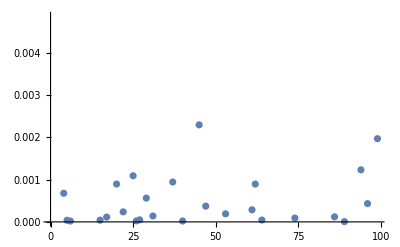

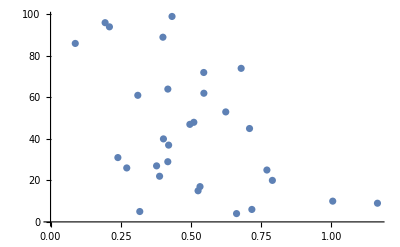

```mathematica
Clear[W4qb,Popa1]
For[Work= Wex;i=1, i<1000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];a4=RandomReal[{0.0001,0.4999}];t=RandomReal[{0,2π}];
Work= Wex; If[Work>0 ,Print[this works];Print[a1];Print[a2];Print[a3];Print[a4];{Popa1[i_]:=Popa1[i]=Abs[a1-a3]+Abs[a3-a2]+Abs[a3-a4];Table[Popa1[i],i];W4qb[i_] :=W4qb[i]= Work;Table[W4qb[i],i]},Null];Clear[Work,a1,a2,a3,a4,t]];
ListPlot[Table[{i,W4qb[i]},{i,100}]]
ListPlot[Table[{Popa1[i],i},{i,100}]]
```

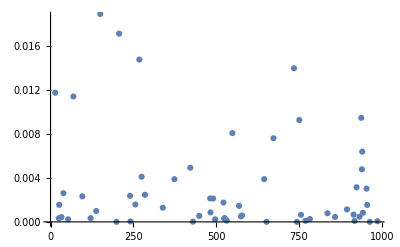
```mathematica
-Graphics-c\03
```

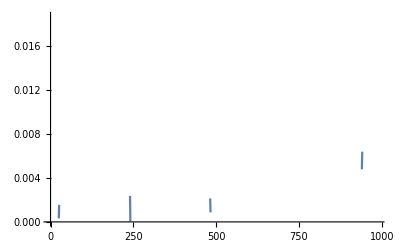

```mathematica
ListLinePlot[Table[{i,W4qb[i]},{i,1000}]]
```

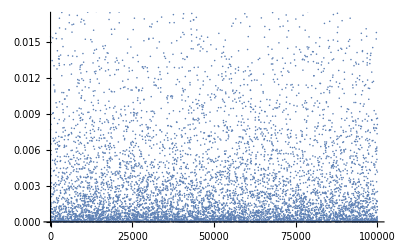

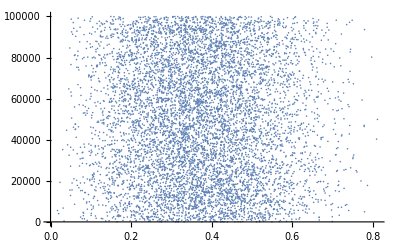

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,Utrial,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_,a4_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}}]
HintTrial = SparseArray[{{4,13}->I,{13,4}->-I},{16,16}];
Utrial=MatrixExp[- I HintTrial  t]//FullSimplify;
RHOTsystrial = Utrial.RHO[a1,a2,a3,a4].Transpose[Utrial]//FullSimplify;
RHOTmachtrial = Utrial.RHO[a2,a2,a3,a4].Transpose[Utrial]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3,a4],{1,3,4}];
Tfinal = TraceSystem[RHOTmachtrial,{2,3,4}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3,a4],{2,3,4}];
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3,4}];
```

```mathematica
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
```

```mathematica
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
```

```mathematica
For[Work= Wex;i=1, i<15,i++,a1=RandomReal[{0,0.5}];a2=RandomReal[{0,0.5}];a3=RandomReal[{0,0.5}];a4=RandomReal[{0,0.5}];t=RandomReal[{0,2π}];
Work= Wex; Print[Work];Clear[Work,a1,a2,a3,a4,t]]
```

-0.0471793

-0.00259779

-0.0140545

-0.00045888

-0.00614344

-6.05687×10^-6

-0.0112478

-0.0266996

-3.3347×10^-7

-0.0419091

-0.0260043

-0.000205066

-0.0118421

-0.989501

```mathematica
A1 =Tfinal[[2,2]]* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = Tfinal[[2,2]]* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
```

```mathematica
WFinal=A1-A2;
```

```mathematica
Wex = WFinal-WInitial;
```

```mathematica
For[Work= Wex;i=1, i<15,i++,a1=RandomReal[{0,0.5}];a2=RandomReal[{0,0.5}];a3=RandomReal[{0,0.5}];a4=RandomReal[{0,0.5}];t=RandomReal[{0,2π}];
Work= Wex; Print[Work];Clear[Work,a1,a2,a3,a4,t]]
```

0.0896663

0.0101749

0.0446598

-0.0366336

-0.176829

0.0349666

-0.0276198

0.0462237

-0.044243

0.0346091

0.0418401

0.0349405

0.032455

0.0221544

```mathematica
Manipulate[Plot[WFinal,{t,0,8}],{a1,0.0001,0.4999},{a4,0.0001,0.4999}]
```

```mathematica
WInitial =  Tinitial[[2,2]]*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  Tinitial[[2,2]]* Tr[RHOthInitial.MatrixLog[RHOthInitial]]//FullSimplify
```

-a3 ((-1+a1+a2-a1 a2) Log[(-1+a1) (-1+a2)]-a1 a2 Log[a1 a2]+a1 (-1+a2) Log[a1-a1 a2]+(-1+a1) a2 Log[a2-a1 a2]+(-1+a3) ((-1+a3) Log[(-1+a3)^2]-2 a3 Log[-(-1+a3) a3])+a3^2 Log[a3^2])

```mathematica
Simplify[WFinal]
```

```mathematica
Wex =FullSimplify[ Tfinal[[2,2]]* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]- Tfinal[[2,2]]* Tr[RHOthFinal.MatrixLog[RHOthFinal]]-( Tinitial[[2,2]]*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  Tinitial[[2,2]]* Tr[RHOthInitial.MatrixLog[RHOthInitial]])]
```

```mathematica
Manipulate[Plot[Wex,{ θ,0,8}],{a1,0,0.5},{a4,0,0.5}]
```

```mathematica
RHOT1 = U1.RHO[a1,a2,a3,a4].Transpose[U1]//FullSimplify;
RHOT2 = U2.RHO[a1,a2,a3,a4].Transpose[U2]//FullSimplify;
RHOT3 = U3.RHO[a1,a2,a3,a4].Transpose[U3]//FullSimplify;
RHOT = RHOT1 +RHOT2+RHOT3
SparseArray[RHOT1];
Lt = Length[ArrayRules[SparseArray[RHOT]]/.Rule->List]-1;
SparsityT = Lt/(2^n)^2 ;cde3
Print[64];
Print[ L];
Print[Lt];
Print[N[Sparsity]];
Print[N[SparsityT]];
```

64

8

0

0.125

0.

For general n-qubit system, we can define a protocol for the allowed interactions in the energy subspaces starting with energy subspace E=1, 2,...n-1. For any energy subspace the energy comes from a qubit being in the 1 state. Therefore, the number of terms per energy subspace can be generated by allowing as many 1’s while all other qubits being in 0. This is a simple nCq combinatorics problem where q = energy subspace. For eg. number of pure states in energy subspace 1 is nC1. Then the number of terms in interaction would be pairwise combination of these temrs without repeating which is simple \sigma (nC1 -1) +(cN1 -2)+(nC1 -3)...+(1). Then the number of correlation produced by these interactions would be double the number of interactions available. So sparsity would be a function of this n as, 
{\Sigma_{E=1}^{n-1} (nCE-1)(nCE) + 2^n}{(2^2n}

# 16-qubit system

SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])

This is my attempt at performing 16 qubit rotations.  We will first begin with defining an uncorrelated initial density matrix for the 16 qubits as:

```mathematica
RHO[a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_,a11_,a12_,a13_,a14_,a15_,a16_] := KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}},{{1-a5,0},{0,a5}},{{1-a6,0},{0,a6}},{{1-a7,0},{0,a7}},{{1-a8,0},{0,a8}},{{1-a9,0},{0,a9}},{{1-a10,0},{0,a10}},{{1-a11,0},{0,a11}},{{1-a12,0},{0,a12}},{{1-a13,0},{0,a13}},{{1-a14,0},{0,a14}},{{1-a15,0},{0,a15}},{{1-a16,0},{0,a16}}]
U
```

```mathematica
U123=KroneckerProduct[U,IdentityMatrix[2],IdentityMatrix[2],IdentityMatrix[2]];
U234=KroneckerProduct[IdentityMatrix[2],U,IdentityMatrix[2],IdentityMatrix[2]];
U345=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],U,IdentityMatrix[2]];
U456=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],IdentityMatrix[2],U];
```

```mathematica
RHO[a1_,a2_,a3_,a4_,a5_,a6_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}},{{1-a5,0},{0,a5}},{{1-a6,0},{0,a6}}];
For[i=1  ; RHOT =RHO,
i<15,
i++;Unitary=RandomChoice[{U123,U234,U345,U456}];ConjUnitary=Transpose[Unitary];RHOT=Unitary.RHOT.ConjUnitary;
RHOT1=TraceSystem[RHOT,{2,3,4,5,6}];
RHOT2=TraceSystem[RHOT,{1,3,4,5,6}];
RHOT3=TraceSystem[RHOT,{1,2,4,5,6}];
RHOT4=TraceSystem[RHOT,{1,2,3,5,6}];
RHOT5=TraceSystem[RHOT,{1,2,3,4,6}];
RHOT6=TraceSystem[RHOT,{1,2,3,4,5}],
Print[RHOT1];Print[RHOT2];Print[RHOT3];Print[RHOT4];Print[RHOT5];Print[RHOT6]]
```

```mathematica
RHO[a1_,a2_,a3_,a4_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}}]
RHO[a1,a2,a3,a4]
```

```mathematica
SparseArray[%66]
```

```mathematica
For[i=1  ; RHOT =RHO,
i<5,
i++;Unitary=RandomChoice[{U123,U234}];ConjUnitary=Transpose[Unitary];RHOT=Unitary.RHOT.ConjUnitary;
RHOT1=TraceSystem[RHOT,{2,3,4}];
RHOT2=TraceSystem[RHOT,{1,3,4}];
RHOT3=TraceSystem[RHOT,{1,2,4}];
RHOT4=TraceSystem[RHOT,{1,2,3}],
Print[RHOT1];Print[RHOT2];Print[RHOT3];Print[RHOT4]]
```

```mathematica
DensityMatrix[q_] := {{1-q,0},{0,q}}
```

```mathematica
Clear[q1,q2,a,b,R]
RelEntBetweenQubits[q1_,q2_,q1t_,q2t_] :=Tr[DensityMatrix[q1].MatrixLog[DensityMatrix[q1]]] - Tr[DensityMatrix[q1].MatrixLog[DensityMatrix[q2]]]-(Tr[DensityMatrix[q1t].MatrixLog[DensityMatrix[q1t]]] - Tr[DensityMatrix[q1t].MatrixLog[DensityMatrix[q2t]]])
RelEntBetweenQubits[0.1,0.3,q1t,q2t]
FreeEn [q1_,q2_,q1t_,q2t_] :=-Temp[q2](Tr[DensityMatrix[q1].MatrixLog[DensityMatrix[q1]]] - Tr[DensityMatrix[q1].MatrixLog[DensityMatrix[q2]]])+Temp[q2t](Tr[DensityMatrix[q1t].MatrixLog[DensityMatrix[q1t]]] - Tr[DensityMatrix[q1t].MatrixLog[DensityMatrix[q2t]]])
```

```mathematica
DistanceBetweenQubits[q1_,q2_,q1t_,q2t_,E_]:=-(Abs[q1t-q2t]+Abs[2q1t-E+q2t]+Abs[2q2t-E+q1t])+Abs[q1-q2]+Abs[2q1-E+q2]+Abs[2q2-E+q1]
DistanceBetweenQubits[0.1,0.3,0.12,0.32,0.8]
FreeEn[0.1,0.3,0.12,0.32]
RelEntBetweenQubits[0.1,0.3,0.12,0.32]
```

0.12

0.00757275

0.00713165

```mathematica
FindInstance[Dis,{q1t,q2t}]
```

$Aborted

```mathematica
Temp[h_]:= 1/(Log[(1-h)/h])
```

```mathematica
RegionPlot3D[ {R-(0.11632-(1-q1t) Log[1-q1t]-q1t Log[q1t]+(1-q1t) Log[1-q2t]+q1t Log[q2t])≥ 0,R-(0.8-Abs[q1t-q2t]-Abs[-0.8+2 q1t+q2t]-Abs[-0.8-q1t+2 q2t])≥0},{q1t,0,0.5},{q2t,0,0.5},{R,0,100}]
```

RegionPlot3D::boolf: {R-(0.11632-Plus[«2»] Log[«1»]-q1t Log[«1»]+(1+Times[«2»]) Log[Plus[«2»]]+q1t Log[q2t])≥0,R-(0.8-Abs[Plus[«2»]]-Abs[Plus[«3»]]-Abs[Plus[«3»]])≥0} must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D[{R-(0.11632-(1-q1t) Log[1-q1t]-q1t Log[q1t]+(1-q1t) Log[1-q2t]+q1t Log[q2t])≥0,R-(0.8-Abs[q1t-q2t]-Abs[-0.8+2 q1t+q2t]-Abs[-0.8-q1t+2 q2t])≥0},{q1t,0,0.5},{q2t,0,0.5},{R,0,100}]

GreaterEqual::nord: Invalid comparison with 0.205474+1.57048 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.000785399+1.57048 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.205474+1.57048 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

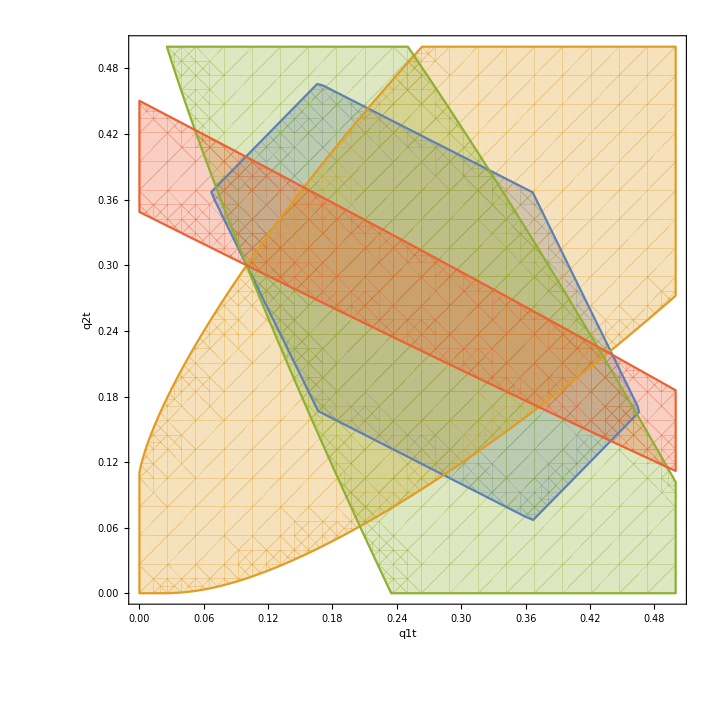

GreaterEqual::nord: Invalid comparison with 0.000785399+1.57048 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

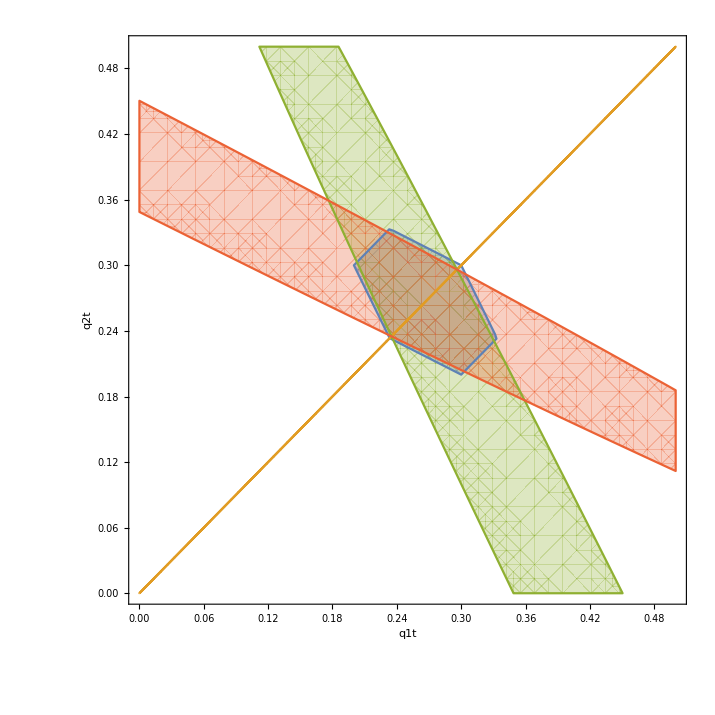

GreaterEqual::nord: Invalid comparison with 0.205474+1.57048 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.000785399+1.57048 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.205474+1.57048 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

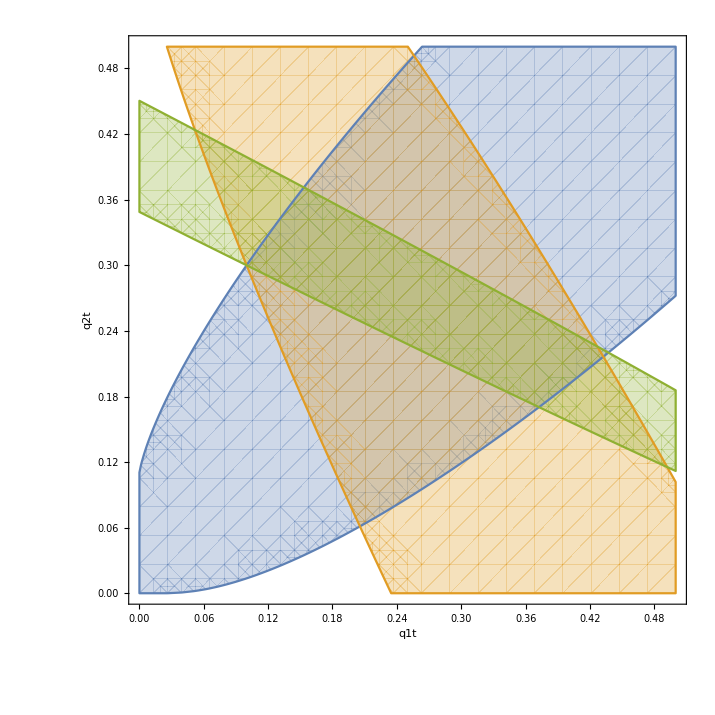

```mathematica
Plot3D[{DistanceBetweenQubits[0.1,0.3,q1t,q2t,0.8],RelEntBetweenQubits[0.1,0.3,q1t,q2t], FreeEn[0.1,0.3,q1t,q2t]},{q1t,0,0.5},{q2t,0,0.5},PlotRange->{0,10}];

RegionPlot[{DistanceBetweenQubits[0.1,0.3,q1t,q2t,0.8]≥ 0,RelEntBetweenQubits[0.1,0.3,q1t,q2t]≥0,RelEntBetweenQubits[0.1,0.4,q1t,0.8-(q1t+q2t)]≥0,RelEntBetweenQubits[0.3,0.4,q2t,0.8-(q1t+q2t)]≥0},{q1t,0.0001,0.4999},{q2t,0.0001,0.4999}, AxesLabel->Automatic]
RegionPlot[{DistanceBetweenQubits[0.3,0.3,q1t,q2t,0.8]≥ 0,RelEntBetweenQubits[0.3,0.3,q1t,q2t]≥0,RelEntBetweenQubits[0.3,0.4,q1t,0.8-(q1t+q2t)]≥0,RelEntBetweenQubits[0.3,0.4,q2t,0.8-(q1t+q2t)]≥0},{q1t,0.0001,0.4999},{q2t,0.0001,0.4999}, AxesLabel->Automatic]

RegionPlot[{RelEntBetweenQubits[0.1,0.3,q1t,q2t]≥0,RelEntBetweenQubits[0.1,0.4,q1t,0.8-(q1t+q2t)]≥0,RelEntBetweenQubits[0.3,0.4,q2t,0.8-(q1t+q2t)]≥0},{q1t,0.0001,0.4999},{q2t,0.0001,0.4999}, AxesLabel->Automatic]
```

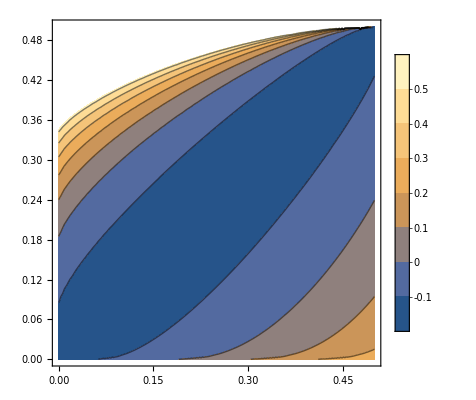

```mathematica
ContourPlot[FreeEn[0.1,0.3,q1t,q2t],{q1t,0.0001,0.4999},{q2t,0.0001,0.4999}, PlotLegends->Automatic]
```

```mathematica
RHOT//FullSimplify;
TargetQubit = TraceSystem[RHOT,{2,3}];
```

```mathematica
PopFinal[a1_,a2_,a3_,θ_] := 1/9 (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))
```

```mathematica
Q2t = PopFinal[a2,a2,a3,θ]//FullSimplify
Q1t = PopFinal[a1,a2,a3,θ]//FullSimplify
```

1/9 (3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+√3 (-1+2 a2) (2 Sin[√3 θ]-Sin[2 √3 θ])))

1/9 (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))

```mathematica
W = WexFinal-WexInitial;

θ=π/4
RegionPlot3D[W≥0,{a1,0.0001,0.4999},{a2,0.0001,0.4999},{a3,0.0001,0.4999}]
ContourPlot3D[{WexFinal,WexInitial},{a1,0.0001,0.4999},{a2,0.0001,0.4999},{a3,0.0001,0.4999}]
```

π/4

-Graphics3D-

```mathematica
WexFinal = Temp[Q2t](Tr[DensityMatrix[Q1t](MatrixLog[DensityMatrix[Q1t]]-MatrixLog[DensityMatrix[Q2t]])])
```

((-Log[1/9 (9-3 (2 a2+a3)-(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))]+Log[1/9 (9-3 (a1+a2+a3)-(4 a1-2 (a2+a3)) Cos[√3 θ]-(2 a1-a2-a3) Cos[2 √3 θ]-√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))]) (1+1/9 (-3 (a1+a2+a3)-(4 a1-2 (a2+a3)) Cos[√3 θ]-(2 a1-a2-a3) Cos[2 √3 θ]-√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ])))+1/9 (-Log[1/9 (3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))]+Log[1/9 (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))]) (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ])))/Log[(9 (1+1/9 (-3 (2 a2+a3)-(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+√3 (-1+2 a2) (2 Sin[√3 θ]-Sin[2 √3 θ])))))/(3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+√3 (-1+2 a2) (2 Sin[√3 θ]-Sin[2 √3 θ])))]

```mathematica
Simplify[WexFinal]
```

((-Log[1/9 (9-3 (2 a2+a3)-(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))]+Log[1/9 (9-3 (a1+a2+a3)-(4 a1-2 (a2+a3)) Cos[√3 θ]-(2 a1-a2-a3) Cos[2 √3 θ]-√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))]) (9-3 (a1+a2+a3)-(4 a1-2 (a2+a3)) Cos[√3 θ]-(2 a1-a2-a3) Cos[2 √3 θ]-√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))+(-Log[1/9 (3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))]+Log[1/9 (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))]) (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ])))/(9 Log[(9-3 (2 a2+a3)-(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))/(3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))])

```mathematica
WexInitial = Temp[a2](Tr[DensityMatrix[a1](MatrixLog[DensityMatrix[a1]]-MatrixLog[DensityMatrix[a2]])]) //FullSimplify
```

(-(-1+a1) (Log[1-a1]-Log[1-a2])+a1 (Log[a1]-Log[a2]))/Log[-1+1/a2]